```mathematica
data={{(2.7032*^-3)/2, 4.4252}, {2 2.2079*^-3, 1.2837}, {19.913*^-3, (.2962+.3215)/2}}
```

{{0.0013516,4.4252},{0.0044158,1.2837},{0.019913,0.30885}}

```mathematica
#[[1]]*#[[2]]&/@data
```

{0.0059811,0.00566856,0.00615013}

```mathematica
(#[[2]])/(2π/#[[1]])&/@data
```

{0.000951922,0.00090218,0.000978824}

```mathematica
kv=Mean[(#[[2]])/(2π/#[[1]])&/@data]
```

0.000944308

```mathematica
f=Integrate[kv ω Sin[ω t],{t,0,θ/ω}]
```

0.000944308-0.000944308 Cos[1. θ]

```mathematica
f/.θ->(2π)/12
```

0.000126513

```mathematica
f2=f(24.5*^6/256)/(3.3/512)(1.24*^3)/(1.24*^3+12.4*^3)//Expand
```

1274.69-1274.69 Cos[1. θ]

```mathematica
θopt=(2π)/12
```

π/6

```mathematica
θopt/Degree//N
```

30.

```mathematica
β=f2/.θ->(2π)/12
```

170.776

```mathematica
α=D[f2,θ]/.θ->θopt
```

637.343

```mathematica
D[√f2,θ]/.θ->θopt
```

24.3854

```mathematica
Δθ=(F-β)/α
```

0.00156901 (-170.776+F)

```mathematica
ω=fclk(60°)/delta
```

(2.56563×10^7)/delta

```mathematica
fclk=24.5*^6
```

2.45×10^7

```mathematica
Δtf=fclk Δθ/ω
```

0.0014983 delta (-170.776+F)

```mathematica
1/0.0014982976492935978
```

667.424

```mathematica
2^20/512.
```

2048.

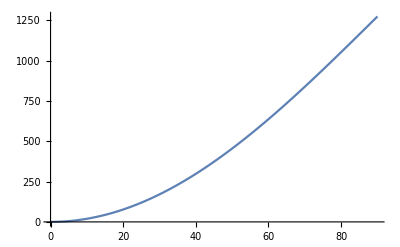

```mathematica
Plot[f2/.θ->θdeg Degree,{θdeg,0,90}]
```

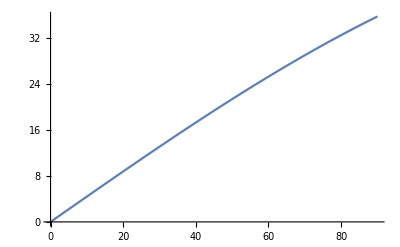

```mathematica
Plot[√f2/.θ->θdeg Degree,{θdeg,0,90}]
```

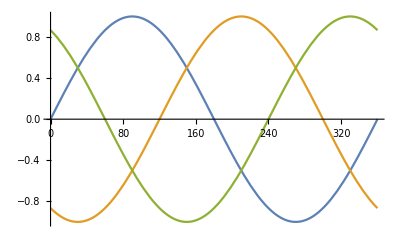

```mathematica
Plot[Evaluate[{Sin[θ],Sin[θ-120°],Sin[θ-240°]}/.θ->θdeg Degree],{θdeg,0,360}]
```

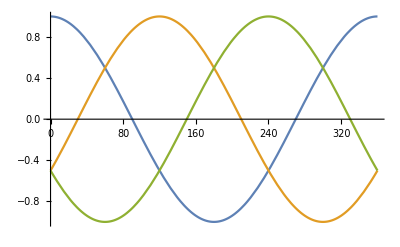

```mathematica
Plot[Evaluate[{Cos[θ],Cos[θ-120°],Cos[θ-240°]}/.θ->θdeg Degree],{θdeg,0,360}]
```

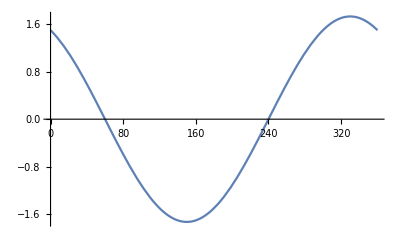

```mathematica
Plot[Evaluate[{Cos[θ]-Cos[θ-120°]}/.θ->θdeg Degree],{θdeg,0,360}]
```

```mathematica
Minimize[Cos[θ]-Cos[θ-120°],θ]//N
```

{-1.73205,{θ→2.61799}}

```mathematica
2.617993877991494/°
```

150.

```mathematica
Maximize[Cos[θ]-Cos[θ-120°],θ]//N
```

{1.73205,{θ→5.75959}}

```mathematica
5.759586531581286/°
```

330.

```mathematica
1/(kv (2π)/rps rps/(60rpm)(1000rpm)/krpm)14
```

141.575 krpm